{}

```mathematica
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\2d_toolbox.wl"]
```

True

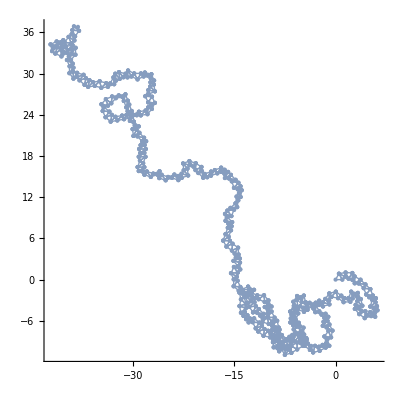

```mathematica
nrods =1000;
shortlength = 0.6;
longlength = 1;
coords = MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]];



CollisionQ[coords,shortlength]
MeshAllTriag[coords,All]
```

Cases when collision occur ed

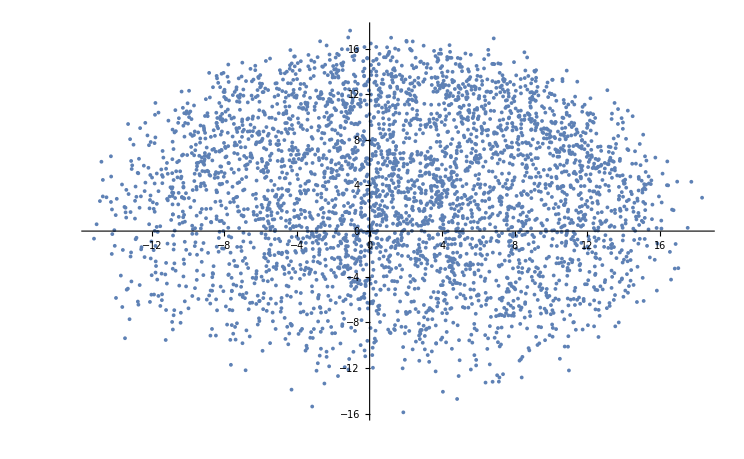

```mathematica
nrods =100;
shortlength = 0.6;
longlength = 1;
coords = Select[Table[MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]],10000],CollisionQ];
endeffector = coords[[All,-1,All]];
ListPlot[endeffector,PlotRange->All]
```

```mathematica
Dimensions[endeffector]
```

{3906,2}

#### Cases when collision did not occur

```mathematica
nrods =100;
shortlength = 0.6;
longlength = 1;
coords = Select[Table[MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]],10000],Not[CollisionQ[#]&]];
endeffector = coords[[All,-1,All]];
ListPlot[endeffector,PlotRange->All]
```

-Graphics-

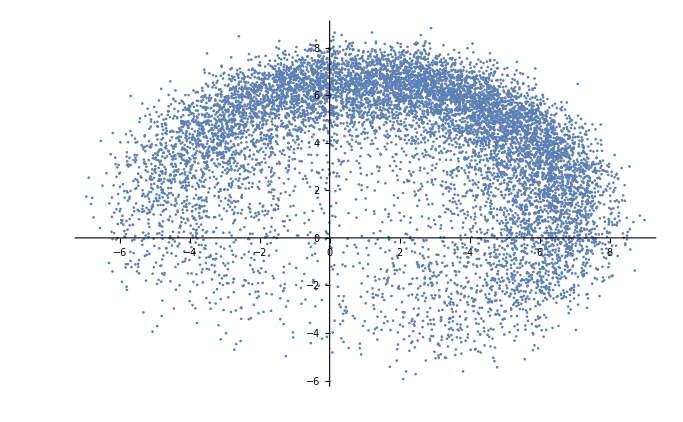

```mathematica
nlen =40;
res = Table[MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{0.6,1},nlen]][[-1]],10000];
ListPlot[res,PlotRange->All]
```

#### Linear time increase with number of required side lengths

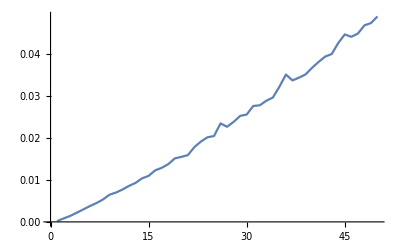

```mathematica
ListLinePlot[Table[First@AbsoluteTiming[MakeTriangleWorm[{0,0},{1,0}, RandomReal[{0.6,1},nlen]];],{nlen,1,5000,100}]]
```

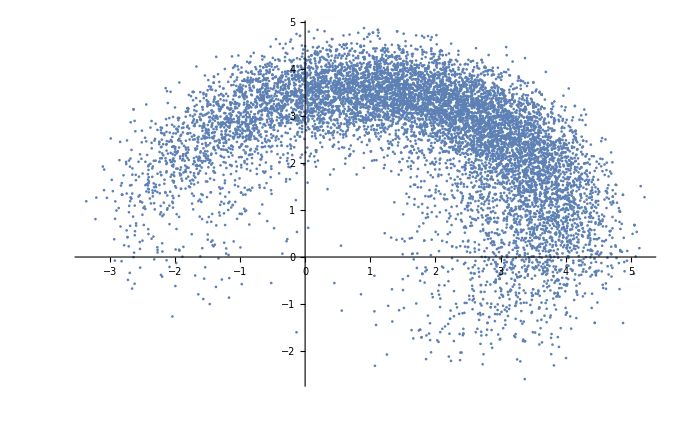

```mathematica
nlen =40;
res = Table[MakeTriangleWorm[{0,0},{1,0}, RandomInteger[{0,1},nlen]*0.4 + 0.6],10000];
Dimensions[res];
endeffector = res[[All,12,All]];
ListPlot[endeffector,PlotRange->All]
```

## Updating states

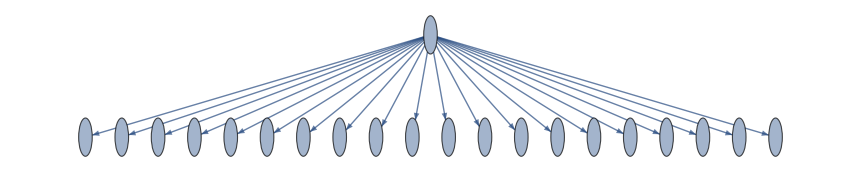

Show::gcomb: Could not combine the graphics objects in ….

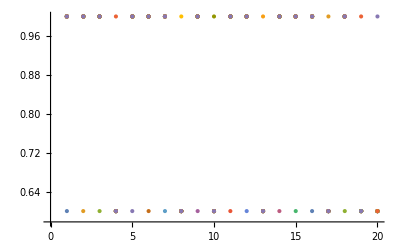
Show[MeshAllTriag[MakeTriangleWorm[{0,0},{1,0},{1,1,1,0.6,1,1,1,0.6,1,0.6,1,1,0.6,1,1,1,0.6,1,0.6,0.6}],All],-Graphics-]

```mathematica
nrods =20;
shortlength = 0.6;
longlength = 1;

fixed1 = {0,0};
fixed2 = {1,0};

possiblestate =  RandomChoice[{shortlength,longlength},nrods];

FlipLength[state_,index_]:=(
neighbour=state;
neighbour[[index]] =state[[index]]/.{0.6->1,1->0.6};
neighbour
)

neighbourstates = Table[FlipLength[possiblestate,i],{i,nrods}]; (*//MatrixForm*)
Graph[possiblestate -> #&/@neighbourstates]

neighbourscoords = MakeTriangleWorm[fixed1,fixed2,#]&/@neighbourstates;
neighboursendeffector = neighbourscoords[[All,-1,All]];

Show[MeshAllTriag[MakeTriangleWorm[fixed1,fixed2,possiblestate],All],ListPlot[neighboursendeffector]]
```

## Updating updated states?

a possible state {initial condition}

{1,1,0.6,1,0.6,0.6,1,1,1,0.6,0.6,0.6}

initial condition neighbours

(0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
1 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
1 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1)

First neighbours' neighbours

(1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
0.6 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
0.6 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1)

-Graphics-

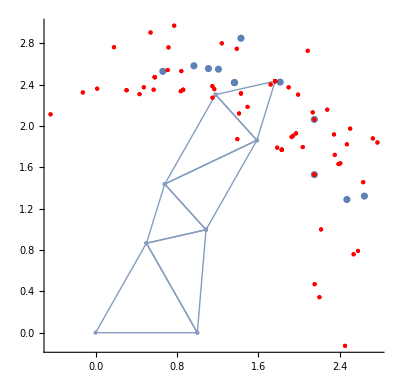

```mathematica
nrods =12;
shortlength = 0.6;
longlength = 1;

fixed1 = {0,0};
fixed2 = {1,0};
(*
ns : neighbours state;
nns : neigbours neighbours states;

nc : neighbours coords;
nnc: neighbours neigbours coords;

ne : neigbours end effector;
nne : neigbours neigbours end effector
*)


Echo["a possible state {initial condition}"];
possiblestate =  MakeState[RandomInteger[2^nrods],nrods]

Echo["initial condition neighbours"];
ns =  FindNeighbours[possiblestate];(*//MatrixForm*)
ns //MatrixForm

Echo["First neighbours' neighbours"];
nns = FindNeighbours/@ns;
nns[[1]]//MatrixForm


g1 =Graph[Join[StateToNeighbours[possiblestate,Green],
Flatten[Table[StateToNeighbours[ns[[i]],Red],{i,Range[nrods]}]]]]

nc = MakeTriangleWorm[fixed1,fixed2,#]&/@ns;
nnc = MakeTriangleWorm[fixed1,fixed2,#]&/@Flatten[nns,1];
ne = nc[[All,-1,All]];
nne = nnc[[All,-1,All]];

g2 =Show[MeshAllTriag[MakeTriangleWorm[fixed1,fixed2,possiblestate],All],ListPlot[ne],ListPlot[nne,PlotStyle->{PointSize[Medium],Red}]]
```

```mathematica
nrods=8;
shortlength=0.6;
longlength=1;
allstates=Tuples[{shortlength,longlength},nrods];
Graph[Flatten[StateToNeighbours[#,Black]&/@allstates]]
```

-Graphics-

```mathematica
nrods = 10;
shortlength = 0.6;
longlength = 1;
fixed1 = {0,0};
fixed2 = {1,0};

maxstates = 2^nrods;
chosenstates = MakeState[#,nrods]&/@RandomInteger[maxstates,100];

transitions = Tooltip[#,PlotCoordTransition[#]]&/@Flatten[StateToNeighbours[#,Black]&/@chosenstates];
Graph[transitions]
```

-Graphics-